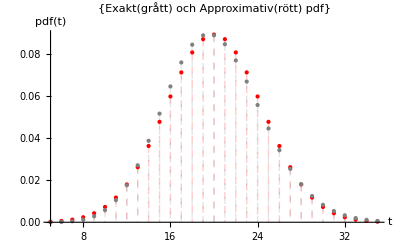

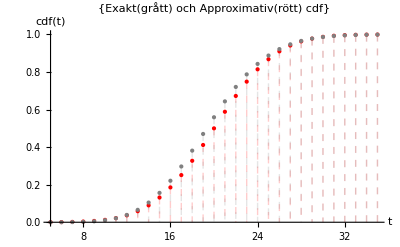

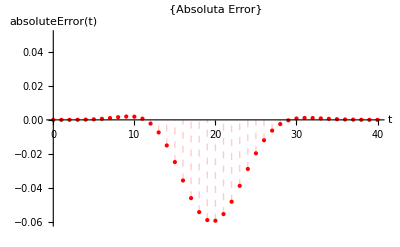

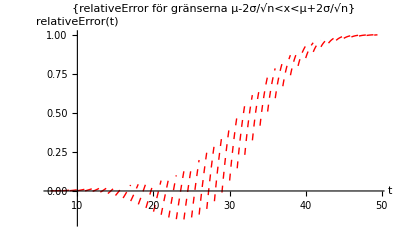

```mathematica
ClearAll["`*"]

(*Exakta fördelningen*)
λ = 1/3; (*förväntade tidsintervall*)
n = 20; (*antalet iid rvs*)
T= 60;

(*exakta fördelningsfunktionen mottagna samtal under en timme *)
(*Inom tidsrymmen T är antalet händelser poissonfördelade*)
poisson = PoissonDistribution[λ *T];
Subscript[μ, exakt]  = Mean[poisson];
σ = StandardDeviation[poisson];

(*Approximativa disti*)
approxi = NormalDistribution[Subscript[μ, exakt] , σ ];

(*P("Absolut fel för X>x") = (1 - P("Exakta sannolikhet för X=<x")) -(1 - P("Approximativa sannolikhet för X=<x"))*)

Pexact[x_] :=N[ (1-CDF[poisson,x])];
Papprox[x_]:= N[ (1-CDF[approxi,x])];
absoluteError[x_] :=  Pexact[x] - Papprox[x] ;

relativeError[x_] := absoluteError[x]/Pexact[x]

(*Plotar pdf, där exakta funktionen är i grå mot normalapproximation svart*)
DiscretePlot[{PDF[approxi,t],PDF[poisson,t]},{t,5,35},PlotStyle->{{Dashed,Red},{Dashed,Gray}},PlotLabel->{"Exakt(grått) och Approximativ(rött) pdf"},AxesLabel->{HoldForm[t],HoldForm[pdf[t]]}, PlotRange->Full]

(*Plot av cdf, där exakta funktionen är i rött mot normalapproximation svart*)
DiscretePlot[{CDF[approxi,t],CDF[poisson,t]},{t,5,35},PlotStyle->{{Dashed,Red},{Dashed,Gray}},PlotLabel->{"Exakt(grått) och Approximativ(rött) cdf"},AxesLabel->{HoldForm[t],HoldForm[cdf[t]]}]


DiscretePlot[{absoluteError[t]},{t,0,40},PlotRange -> {-.06,.05},PlotStyle->{{Dashed,Red},{Dashed,Gray}},PlotLabel->{"Absoluta Error"},AxesLabel->{HoldForm[t],HoldForm[absoluteError[t]]}]

(*Plot av Relative Error*)
Plot[{relativeError[x]},{x, N[(Subscript[μ, exakt] -2σ) (√n)],N[(Subscript[μ, exakt] +2σ)/(√n)]},PlotRange -> {-.2,1},PlotStyle->{{Dashed,Red},{Dashed,Gray}},PlotLabel->{"relativeError för gränserna μ-2σ/√n<x<μ+2σ/√n"},AxesLabel->{HoldForm[t],HoldForm[relativeError[t]]}]
```